This notebook is for generating plots from the data generated by ChiralAnomaly_PTB.nb

Flux tube is shown in blue . The charge density is summed over in the common region which is between both the red and the green lines

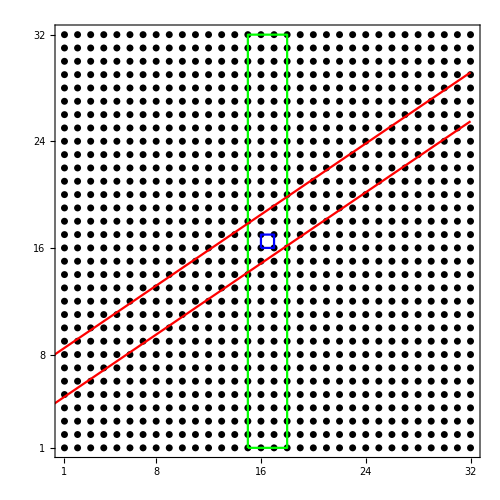
```mathematica
-Graphics-;
```

```mathematica
(** Equations of Lines **)
```

```mathematica
LineUpIrrational[x_]:=(2/(1+Sqrt[5]))*(x-1)+8.5
LineDnIrrational[x_]:=(2/(1+Sqrt[5]))*(x-2)+5.5
LineUpRational[x_]:=(2/3)*(x-1)+8.5
LineDnRational[x_]:=(2/3)*(x-2)+5.5
```

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------*)
```

Here, we gather data for an irrational PTB (in a 32x32 parent system), for different values of magnetic field, generated by ChiralAnomaly_PTB.nb

We store in the form {ϕ/ϕ_0, Q}

```mathematica
dataQ32x32Irrational = {{0,47.12388980384696},{0.02,47.15532629260679},{0.04,47.18674594707946},{0.06,47.21814495178946},{0.08,47.24951271269278},{0.1,47.28083847798042}}
```

{{0,47.1239},{0.02,47.1553},{0.04,47.1867},{0.06,47.2181},{0.08,47.2495},{0.1,47.2808}}

We remove the background charge, to get {ϕ/ϕ_0,δQ}

```mathematica
dataDeltaQIrrational = Table[{dataQ32x32Irrational[[i]][[1]],dataQ32x32Irrational[[i]][[2]] - dataQ32x32Irrational[[1]][[2]]},{i,1,Dimensions[dataQ32x32Irrational][[1]]}]
```

{{0,0.},{0.02,0.0314365},{0.04,0.0628561},{0.06,0.0942551},{0.08,0.125623},{0.1,0.156949}}

Here we fit the data to get the slope

```mathematica
slopeIrrational = D[Fit[dataDeltaQIrrational,{k},k],k]
```

1.57014

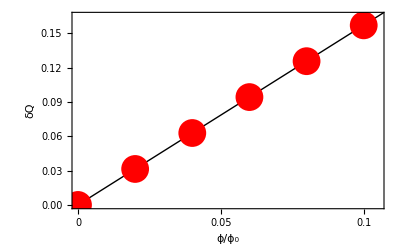

```mathematica
Show[Plot[π*x/2,{x,0,0.3},PlotStyle->{Black,Thick}],ListPlot[dataDeltaQIrrational,PlotStyle->{PointSize[0.05],Red}],PlotRange->{{0,0.105},{0,0.165}},
Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{ϕ/Subscript[ϕ, 0],δQ},RotateLabel->False,FrameTicks->{{0,0.05,0.1},Automatic,{},{}}]
```

We compare the slope with theoretical value of π/2

```mathematica
N[slopeIrrational /(π/2)]
```

0.999579

```mathematica
(**-----------------------------------------------------------------------------------------------------------------------------**)
```

Here, we gather data for a rational PTB (in a 32x32 parent system), for different values of magnetic field, generated by ChiralAnomaly_PTB.nb

We store in the form {ϕ/ϕ_0, Q}

```mathematica
dataQ32x32Rational = {{0,43.982297150257125},{0.02,44.013652311459765},{0.04,44.04499709006855},{0.06,44.07632060659586},{0.08,44.10761203911954},{0.1,44.13886047358382}}
```

{{0,43.9823},{0.02,44.0137},{0.04,44.045},{0.06,44.0763},{0.08,44.1076},{0.1,44.1389}}

We remove the background charge, to get {ϕ/ϕ_0,δQ}

```mathematica
dataDeltaQRational = Table[{dataQ32x32Rational[[i]][[1]],dataQ32x32Rational[[i]][[2]] - dataQ32x32Rational[[1]][[2]]},{i,1,Dimensions[dataQ32x32Rational][[1]]}]
```

{{0,0.},{0.02,0.0313552},{0.04,0.0626999},{0.06,0.0940235},{0.08,0.125315},{0.1,0.156563}}

Here we fit the data to get the slope

```mathematica
slopeRational = D[Fit[dataDeltaQRational,{k},k],k]
```

1.56627

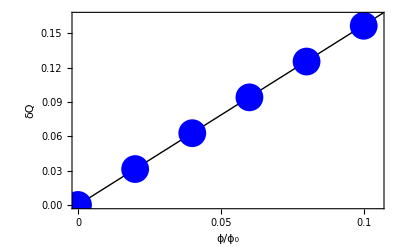

```mathematica
Show[Plot[π*x/2,{x,0,0.3},PlotStyle->{Black,Thick}],
ListPlot[dataDeltaQRational,PlotStyle->{PointSize[0.05],Blue}],PlotRange->{{0,0.105},{0,0.165}},
Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},RotateLabel->False,FrameLabel->{ϕ/Subscript[ϕ, 0],δQ},FrameTicks->{{0,0.05,0.1},Automatic,{},{}}]
```

We compare the slope with theoretical value of π/2

```mathematica
N[slopeRational /(π/2)]
```

0.997121